```mathematica
SetOptions[$FrontEndSession,AutoStyleOptions->{"SymbolContextStyles"->{"global`"->Purple}}]

AppendTo[$ContextPath,"global`"];
```

## Functions

### Importing

```mathematica
BuildFilePath[root_,date_,file_]:=root<>date<>"/"<>file<>"/"<>file<>".txt"
```

```mathematica
ImportDataFile[pathToFile_]:=Module[{nans,rawData},
nans=ConstantArray["nan",4];
rawData=Import[pathToFile,"Data"];
Rest/@Most@Split[Prepend[rawData,nans],(#2=!=nans)&]
]
```

```mathematica
ImportDataFiles[pathToFiles_]:=Join@@(ImportDataFile/@pathToFiles)
```

### Cleaning

```mathematica
CompensateDetectorLags[data_,lags_,lenStirap_]:=Module[{rules},

rules=Append[Rule@@@MapAt[N,lags,{All,2}],_Integer:>0];

Function[{m},
With[{ls=m[[;;,1]]/.rules},
Transpose[{
m[[;;,1]],
Mod[m[[;;,2]]-ls,lenStirap],
m[[;;,3]]-ls,
m[[;;,4]]-UnitStep[ls-m[[;;,2]]]
}]
]
]/@data
]
```

### Filtering

```mathematica
FilterByCriteria[data_,crit_,results_]:=Transpose[
Function[{m},
Table[
SelectFirst[GatherBy[m,crit],crit[#[[1]]]==res&,{}],
{res,results}
]
]/@data
]

FilterByDetector[data_,detectors_]:=FilterByCriteria[data,(#[[1]]&),detectors]
```

### Statistics

```mathematica
HomCorrelations[data_,detPairs:{{_Integer,_Integer}..},func_:Subtract]:=Module[{assoc,emptyAssoc,flatRiffledData,ditheredDiffs,homBunches,groupbyInput},

flatRiffledData=Join@@Riffle[DeleteCases[data,{}],{{{-1,-1,-1,-1}}}];
ditheredDiffs=(Prepend[#,1]*Append[#,1])&@Differences[flatRiffledData[[;;,4]]];
homBunches=SplitBy[Pick[flatRiffledData,ditheredDiffs,0],Last];
groupbyInput=Transpose/@Flatten[Subsets[#,{2}]&/@homBunches,1];

assoc=GroupBy[groupbyInput,First->(#[[2]]&)];

emptyAssoc=AssociationThread[#->ConstantArray[{},Length[#]]]&@Union[detPairs,Reverse/@detPairs];
assoc=Merge[{assoc,emptyAssoc},Flatten[#,1]&];

Map[func@@#&,
If[SameQ@@#,assoc[#],Flatten[{assoc[#],Reverse/@assoc[Reverse@#]},1]]&/@detPairs,
{2}
]
]
```

```mathematica
Correlations[data_,det1_,det2_,column_:3]:=
Flatten[
Outer[Plus,#[[1,;;,column]],-#[[2,;;,column]]]&/@Transpose[FilterByDetector[data,{det1,det2}]]
]
```

```mathematica
WindowedCounts[data_,atomWindow_,backWindow_]:=Module[{nReal,nBack},

nReal=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,atomWindow]];
nBack=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,backWindow]];

nBack=(Subtract@@-atomWindow)/(Subtract@@-backWindow)nBack;

{nReal-nBack,nBack}
]
```

```mathematica
RealPhotonsPerThrow[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,atomWindow]];
nBack=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,backWindow]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=scaleFactor{nBack,σBack}/Length[data];

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
NCorrelationsPerThrow[data_,detectors_List,idx_List,idxBack_List:Range[101,200]]:=Module[{correls,countsDet1,countsDet2,backCorrels},

{correls,backCorrels}=Transpose[
Table[
Total/@{#[[idx]],#[[idxBack]]}&@SparseArray[Rule@@@Tally[Select[Correlations[data,i,j,4],Positive]],{25000}],{i,detectors},{j,detectors}],
{2,3,1}
];

backCorrels=backCorrels/(Length[idxBack]/Length[idx]);

N@Transpose[{correls-backCorrels,√(correls+backCorrels)}/Length[data],{3,1,2}]
]
```

```mathematica
TotalCorrelationsPerThrow[data_,det1_,det2_]:=UncertaintySum@@Flatten[NCorrelationsPerThrow[data,{det1,det2},Range[100]],1]

PM1CorrelationsPerThrow[data_,det1_,det2_]:=UncertaintySum@@Flatten[NCorrelationsPerThrow[data,{det1,det2},{1}],1]
```

### Plotting

```mathematica
LabelledMOTHistogram[data_,atomLims_,notAtomLims_]:=Module[{binWidth,nNotAtoms,backLevel,nBins=50},

nNotAtoms=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,notAtomLims]];
backLevel= nNotAtoms/(nBins((#[[2]]-#[[1]]&)@notAtomLims)/25000);
backLevel=backLevel/(Length[data](25000 photonLength 10^-12/10^-3)/nBins);

Histogram[Flatten[data[[;;,;;,4]]],{0,25000,25000/nBins},Function[{bins,counts},counts/(Length[data](25000 photonLength 10^-12/10^-3)/nBins)],
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^9}]&@Range[0,25000,5000]}},
Epilog->{
Dashed,Line[{{0,backLevel},{25000,backLevel}}],Opacity[0.2],
Green,Rectangle[Scaled[{atomLims[[1]]/25*^3,0}],Scaled[{atomLims[[2]]/25*^3,1}]],Red,Rectangle[Scaled[{notAtomLims[[1]]/25*^3,0}],Scaled[{notAtomLims[[2]]/25*^3,1}]]
},
FrameLabel->{{"Counts per Throw per ms",None},{"Pulse Number","MOT time / ms"}},
AspectRatio->1/2,
genOpts
]
]
```

```mathematica
LabelledG2Histogram3[data_,det1_,det2_]:=Module[{correls11,correls12,correls22,max},

correls11=DeleteCases[Correlations[data,det1,det1,4],0];
correls12=Correlations[data,det1,det2,4];
correls22=DeleteCases[Correlations[data,det2,det2,4],0];

max=Max[HistogramList[#,{-binLimit-(binWidth/2),binLimit+(binWidth/2),binWidth}][[2]]&/@{correls11,correls12,correls22}];
max=5Ceiling[max/5.]/Length[data];

{
Histogram[{Select[correls11,EvenQ],Select[correls11,OddQ]},{-binLimit-(binWidth/2),(binWidth/2),binWidth},Function[{bins,counts},counts/Length[data] ],
PlotRange->{All,{0,max}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},ChartStyle->{ColorData[97][4],ColorData[97][1]},AspectRatio->1,
genOpts],
Histogram[{Select[correls12,EvenQ],Select[correls12,OddQ]},{-binLimit-(binWidth/2),binLimit+(binWidth/2),binWidth},Function[{bins,counts},counts/Length[data] ],
PlotRange->{All,{0,max}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},ChartStyle->{ColorData[97][4],ColorData[97][1]},AspectRatio->1/2,
genOpts],
Histogram[{Select[correls22,EvenQ],Select[correls22,OddQ]},{-(binWidth/2),binLimit+(binWidth/2),binWidth},Function[{bins,counts},counts/Length[data] ],
PlotRange->{All,{0,max}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},ChartStyle->{ColorData[97][4],ColorData[97][1]},AspectRatio->1,
genOpts]
}
]
```

```mathematica
LabelledSTIRAPHistogram[data_,atomWindow_,backWindow_,label_]:=Module[{nReal,nBack,darkRate,dataWindowed,nBins=20},

{nReal,nBack}=WindowedCounts[data,atomWindow,backWindow];

darkRate=nBack/((Subtract@@-atomWindow) photonLength 10^-12 Length[data]);

dataWindowed=Function[{m},Select[m,Between[#[[4]],atomWindow]&]]/@data;

Histogram[Flatten[dataWindowed[[;;,;;,2]]]/1.*^3,{0,photonLength,photonLength/nBins}/1.*^3,
FrameLabel->{{"Occurances",None},{"Detection Time / ns",label}},
AspectRatio->1,
ImageSize->220,
Epilog->{
{Dashed,Line[{{0,nBack/nBins},{photonLength/1000,nBack/nBins}}]},
Text["Counts Real = "<>ToString[nReal],Scaled[{0.05,0.95}],Scaled[{0,1}],Background->Directive[Opacity[0.8],White]],
Text["Counts Dark = "<>ToString[nBack],Scaled[{0.05,0.85}],Scaled[{0,1}],Background->Directive[Opacity[0.8],White]],
Text["Dark Rate = "<>ToString[darkRate],Scaled[{0.05,0.75}],Scaled[{0,1}],Background->Directive[Opacity[0.8],White]]
},
genOpts]
]
```

```mathematica
StirapSubHistogram[data_,atomWindow_,backWindow_,nbins_,opts:OptionsPattern[Histogram]]:=Module[{dataAtom,dataBack,nAtom,nBack,σAtom,σBack},

dataAtom=Function[{m},Select[m,Between[#[[4]],atomWindow]&]]/@data;
dataBack=Function[{m},Select[m,Between[#[[4]],backWindow]&]]/@data;

nAtom=N@Length[Flatten[dataAtom[[;;,;;,2]]]];
nBack=N@Length[Flatten[dataBack[[;;,;;,2]]]];

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=(Subtract@@atomWindow)/(Subtract@@backWindow){nBack,σBack}/Length[data];

Histogram[Flatten[dataAtom[[;;,;;,2]]]/1000,{0,photonLength,photonLength/nbins}/1000,Function[{bins,counts},counts/(Length[data] photonLength/nbins 10^-6)],
opts,
Epilog->{
{Opacity[0.5],Black,Rectangle[{0,0},{photonLength/1000,(nBack/nbins)/( photonLength/nbins 10^-6)}]},
(*{First@Plot[((nBack/nbins)/( photonLength/nbins 10^-6))+50 Sin[π x/(photonLength/1000)]^2,{x,0,photonLength/1000}]},*)
{Text[StringRiffle[UncertaintyForm[#,1]&/@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}},"\n"],Scaled[{0.98,0.98}],Scaled[{1,1}],Background->Directive[Opacity[1],White]]}
}
]

]
```

### Formatting

```mathematica
UncertaintyForm[{a_,b_},p_:2]:=NumberForm[
SetAccuracy[a±b,Accuracy@SetPrecision[b,p]],
NumberFormat->(If[#3=!="",StringJoin[{#1,Table["0",Abs@ToExpression@#3-1]}],#1]&),
ExponentFunction->(Null&)
]//ToString//Quiet
```

```mathematica
PadDecimalStrings[string_,{l1_,lt_}]:=StringRiffle[
StringPadRight[StringRepeat[" ",l1-With[{sp=StringPosition["0","."]},If[sp==={},StringLength["0"],sp[[1,1]]]]]<>#,lt]&/@StringSplit[string][[{1,-1}]],
"±"]
```

### Derived Statistics

```mathematica
AtomsPerThrowPM1[Np_,Nc1_,T_]:=(Np^2(T-1))/(Nc1 T^2)
PhotonEfficiencyPM1[Np_,Nc1_,T_]:=(Nc1 T)/(Np (T-1))
```

```mathematica
AtomsPerThrowPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Np^2(T-1))/(Nc1 T^2),(T-1)/T^2 Np^2/Nc1 √(((2Np σNp)/Np^2)^2+(σNc1/Nc1)^2)}
PhotonEfficiencyPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Nc1 T)/(Np (T-1)),T/(T-1)Nc1/Np √((σNc1/Nc1)^2+(σNp/Np)^2)}
```

```mathematica
AtomsPerThrow[Np_,NcAll_,T_]:=(Np^2(T-1))/(2 NcAll T)
PhotonEfficiency[Np_,NcAll_,T_]:=(2 NcAll)/(Np (T-1))
```

```mathematica
AtomsPerThrow[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(Np^2(T-1))/(2 NcAll T),(T-1)/(2 T)Np^2/NcAll √(((2Np σNp)/Np^2)^2+(σNcAll/NcAll)^2)}
PhotonEfficiency[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(2 NcAll)/(Np (T-1)),2/(T-1)NcAll/Np √((σNcAll/NcAll)^2+(σNp/Np)^2)}
```

## Usage New

ToDo:
	Handle when attempting to import files which aren’t there or have no data
	Make it so that the only files listed as available to import are folder with actual data txt files in (as the folder grets created at the start of a run and the txt file at the end. (or not, Tom lines them up early)
	FIgure / fix importing many many file (20+ files, 4000+ runs)
	Including when also selsected empty folders...

### Import New

```mathematica
folderForm=__~~"-"~~__~~"-"~~__;
```

```mathematica
root="path to data folders";
root="Z:\\Results017_New\\data\\";
```

```mathematica
root="/Volumes/ALDAQ/KuhnGroup/Results017_New/data/";
```

```mathematica
Panel[
Column[{
Labeled[
InputField[Dynamic[root],String],
"Root",Top],
Labeled[
PopupMenu[Dynamic[date],Reverse@(FileNameTake/@FileNames[folderForm,root])],
"Date",Left],
Labeled[Row[{
Dynamic@ListPicker[Dynamic[files],Reverse@(FileNameTake/@FileNames[folderForm,root<>date])],
Column[{
Button["Update",odate=date;date="00-00-00";date=odate;,ImageSize->{80,80}],
Button["Copy File Names",CopyToClipboard[StringRiffle[files,", "]]]
}]
}],
"Files",Left],
Button["Import",
data1Raw=ImportDataFiles[BuildFilePath[root,date,#]&/@files];,
Method->"Queued"
],

Dynamic["Length data = "<>ToString[Length[data1Raw]]]
}]
]
```

Root
Date
Update
Copy File NamesFiles
Import

### Display New

```mathematica
sliderOpts=Sequence[Method->"Push",MinIntervalSize->500,ImageSize->{275,20}];

Panel[
Grid[{{

Column[{
IntervalSlider[Dynamic[atomWindow],{0,25000,500},Appearance -> {"ThumbAppearance" -> {Dynamic[Framed[First[atomWindow],Background->LightGreen]],None,Dynamic[Framed[Last[atomWindow],Background->LightGreen]]}},sliderOpts],
Histogram[Flatten[data[[;;,;;,4]]],{0,25000,500},ImageSize->300,Frame->True,GridLines->Automatic,PlotRangePadding->None,Epilog->{Opacity[0.2],Green,Dynamic[Rectangle @@ Scaled/@Thread[{atomWindow/25000,{0,1}}]],Red,Dynamic[Rectangle @@ Scaled/@Thread[{backWindow/25000,{0,1}}]]}],
IntervalSlider[Dynamic[backWindow],{0,25000,500},Appearance -> {"ThumbAppearance" -> {Dynamic[Framed[First[backWindow],Background->LightRed]],None,Dynamic[Framed[Last[backWindow],Background->LightRed]]}},sliderOpts]
},Alignment->Center],

Column[{
Labeled[TogglerBar[Dynamic[detectors],Range[0,7]],"Detectors",Top],
Dynamic@Labeled[
Activate@Grid@Transpose@ArrayReshape[
Table[Labeled[
Inactivate@InputField[Dynamic[lag[i]],Number,Enabled->MemberQ[detectors,i],Appearance->"Framed",Background->GrayLevel[1-0.2Boole@Not@MemberQ[detectors,i]],ImageSize->50],ToString[i],Left
],{i,0,7}],
{2,4}],"Lags / ps",Top
]
},Alignment->Center,Spacings->2],

Column[{
Labeled[InputField[Dynamic[countCutOff],Number,ImageSize->150],"Count Cut-Off",Top],
Labeled[InputField[Dynamic[photonLength],Number,ImageSize->150],"Photon Length / ps",Top],
Labeled[InputField[Dynamic[tInter],Number,ImageSize->150],"Interaction Time / pulses",Top]
},Spacings->2]

},{SpanFromAbove,Null,SpanFromLeft},{SpanFromAbove,Button["Analyse",analysis=Analyse[],ImageSize->{200,50}],SpanFromLeft}},Spacings->2,Alignment->Top]
]
```

-Graphics-
 |  |  |  |  |  |  |  | Detectors
 | Count Cut-Off
Photon Length / ps
Interaction Time / pulses
 |  | 
 | Analyse |

```mathematica
Dynamic[analysis]
```

```mathematica
genOpts=Sequence[PlotRange->All,Frame->True,GridLines->Automatic,PlotRangePadding->None,ImageSize->Medium];
```

```mathematica
Analyse[]:=Module[{},

binLimit=100;
binWidth=1;

data2=Select[data,Length[#]<countCutOff&];

p1=LabelledMOTHistogram[data2,atomWindow,backWindow];

{Np,σNp}=RealPhotonsPerThrow[data,atomWindow,backWindow][[1]];

data2=Function[{m},Select[m,Between[#[[4]],atomWindow]&]]/@data2;
data2=CompensateDetectorLags[data2,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];

p2=ListLinePlot[Length/@data2,FrameLabel->{"Throw Number","Counts"},genOpts];
p3=Histogram[Length/@data2,FrameLabel->{"Counts","Occurances"},genOpts];

{p4,p5}=Histogram[Flatten[#[[1,;;,;;,2]]]/1.*^3,{0,photonLength,photonLength/21}/1.*^3,FrameLabel->{"Detection Time / ns","Occurances"},AspectRatio->1,ImageSize->Small,Epilog->{Text["Counts "<>#[[2]]<>"= "<>ToString[Length[Flatten[#[[1,;;,;;,2]]]]],Scaled[{0.05,0.95}],Scaled[{0,1}],Background->White]},genOpts]&/@Transpose[{FilterByDetector[data2,dets],{"Det 0","Det 4"}}];

{p7,p8}=Histogram[Flatten[#[[1,;;,;;,2]]]/1.*^3,{0,photonLength,photonLength/21}/1.*^3,FrameLabel->{"Detection Time / ns","Occurances"},AspectRatio->1,ImageSize->Small,Epilog->{Text["Counts "<>#[[2]]<>"= "<>ToString[Length[Flatten[#[[1,;;,;;,2]]]]],Scaled[{0.05,0.95}],Scaled[{0,1}],Background->White]},genOpts]&/@Transpose[{FilterByCriteria[data2,(EvenQ[#[[4]]]&),{True,False}],{"Even","Odd"}}];

{p6}=LabelledG2Histogram[data2,detectors[[1]],detectors[[2]]];

{Nc,σNc}=TotalCorrelationsPerThrow[data2,detectors[[1]],detectors[[2]]];

infoTable=TableForm[{
{"Interaction Time:", tInter},
{"",""},
{"Number MOT Throws:", $NTHROWS},
{"Real photons per throw:", Np,σNp},
{"Correlations per throw", Nc,σNc},
{"",""},
{"Atoms per throw:",Sequence@@AtomsPerThrow[{Np,σNp},{Nc,σNc},tInter]},
{"Photon efficiency:",Sequence@@PhotonEfficiency[{Np,σNp},{Nc,σNc},tInter]}
}];


Grid[{
{p1,p6},
{p2,infoTable},
{p3,Grid[{{p4,p5},{p7,p8}}]}
}]

]
```

### Display Old

```mathematica
genOpts=Sequence[PlotRange->All,Frame->True,GridLines->Automatic,PlotRangePadding->None,ImageSize->{Automatic,320}];
```

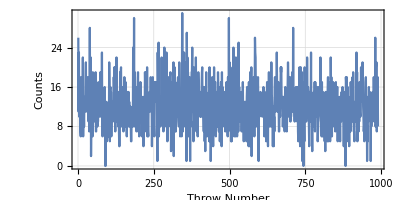
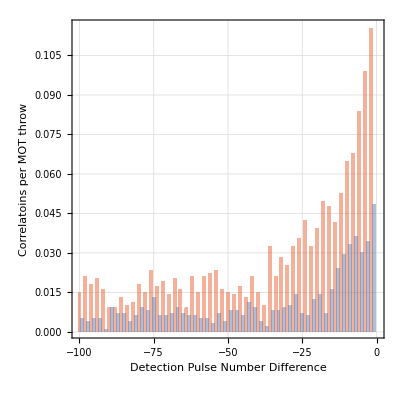
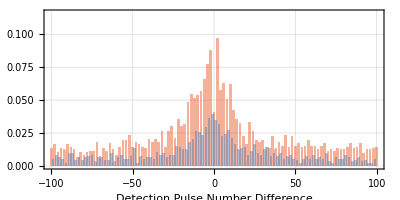
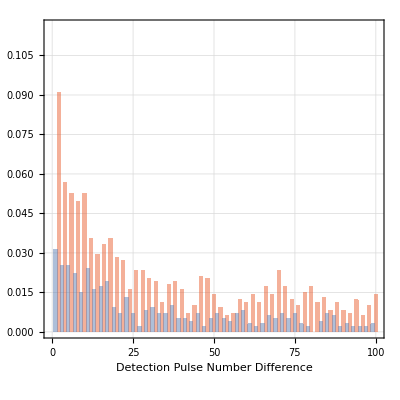
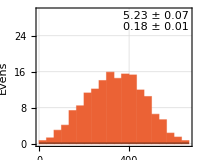
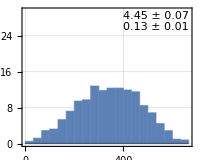
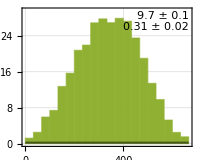
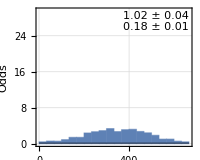
-Graphics- | -Graphics-
-Graphics--Graphics--Graphics- | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Inset numbers of 'real' detections (background corrected) and background detections, per throw. | Interaction Time: | 30  ⟺  19.98 μs
 | 
Number MOT Throws: | 990
 | 
Real photons per throw: |     11.62   ±    0.11    
All Correlations per throw |     2.64    ±    0.10    
±1 Correlations per throw |     0.113   ±    0.014   
 | 
Atoms per throw: |     24.7    ±    1.1     
Photon efficiency: |     0.01569 ±    0.00064

```mathematica
countCutOffs={1,100};

atomWindow={2.5,9.5}10^3;
backWindow={15.5,24.5}10^3;

detectors={0,2};
lag[0]=60.*^3;lag[2]=60.*^3;

photonLength=666.*^3;

tInter=30;

binLimit=100;
binWidth=1;


data2Limited=Select[data1Raw,Between[Length[#],countCutOffs]&];
global`$NTHROWS=Length[data2Limited];

p1=LabelledMOTHistogram[data2Limited,atomWindow,backWindow];

{Np,σNp}=RealPhotonsPerThrow[data2Limited,atomWindow,backWindow][[1]];

data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];
data3Windowed=Function[{m},Select[m,Between[#[[4]],atomWindow]&]]/@data2Limited;


p2=ListLinePlot[Length/@data3Windowed,FrameLabel->{{"Counts",None},{"Throw Number",""}},PlotRange->{0,All},FrameTicks->{Automatic,{Automatic,All}},AspectRatio->1/2,genOpts];


subdividedData=FilterByCriteria[#,(EvenQ[#[[4]]]&),{True,False}]&/@FilterByDetector[data2Limited,detectors];

subdividedDataDetectors=Map[Join@@#&,Transpose/@subdividedData,{2}];
subdividedDataParities=Map[Join@@#&,Transpose/@Transpose[subdividedData],{2}];


With[{nbins=20},
max=Max[HistogramList[Flatten[#[[;;,;;,2]]],{0,photonLength,photonLength/20}][[2]]&/@Join[subdividedDataParities,subdividedDataDetectors]];
hopts=Sequence[Frame->True,GridLines->Automatic,PlotRangePadding->None,PlotRange->{All,{0,5Ceiling[max/5.]/($NTHROWS photonLength/nbins 10^-6)}},ImageSize->200,AspectRatio->0.8];

g3=Grid[
{{
StirapSubHistogram[subdividedData[[1,1]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][4],FrameLabel->{{"Evens",None},{None,"Detector 0"}},hopts],
StirapSubHistogram[subdividedData[[2,1]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][1],FrameLabel->{{"",None},{None,"Detector 1"}},hopts],StirapSubHistogram[subdividedDataParities[[1]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][3],FrameLabel->{{"",None},{None,"Both Detectors"}},hopts]
},{
StirapSubHistogram[subdividedData[[1,2]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][1],FrameLabel->{{"Odds",None},{None,""}},hopts],
StirapSubHistogram[subdividedData[[2,2]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][4],FrameLabel->{{"Counts per Throw per μs.",None},{None,""}},hopts],
StirapSubHistogram[subdividedDataParities[[2]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][3],FrameLabel->{{"",None},{None,""}},hopts]
},{
StirapSubHistogram[subdividedDataDetectors[[1]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][2],FrameLabel->{{"Both Parities",None},{None,""}},hopts],
StirapSubHistogram[subdividedDataDetectors[[2]],atomWindow,backWindow,nbins,ChartStyle->ColorData[97][2],FrameLabel->{{"",None},{None,""}},hopts],
Framed@TextCell["Inset numbers of 'real' detections (background corrected) and background detections, per throw."]
}},
ItemSize->14
];
];


{p4,p5}=LabelledSTIRAPHistogram[#[[1]],atomWindow,backWindow,#[[2]]]&/@Transpose[{FilterByDetector[data2Limited,detectors],{"Detector 0 - All","Detector 1 - All"}}];
{p7,p8}=LabelledSTIRAPHistogram[#[[1]],atomWindow,backWindow,#[[2]]]&/@Transpose[{FilterByCriteria[data2Limited,(EvenQ[#[[4]]]&),{True,False}],{"Even","Odd"}}];

p6=LabelledG2Histogram3[data3Windowed,detectors[[1]],detectors[[2]]];

{NcAll,σNcAll}=TotalCorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];
{Nc1,σNc1}=PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];

pads={5,12};

infoTable=TableForm[{
{"Interaction Time:", ToString[tInter]<>"  ⟺  "<>ToString[tInter photonLength/10^6]<>" μs"},
{"",""},
{"Number MOT Throws:", Length[data2Limited]},
{"",""},
{"Real photons per throw:", PadDecimalStrings[UncertaintyForm[{Np,σNp}],pads]},
{"All Correlations per throw",  PadDecimalStrings[UncertaintyForm[{NcAll,σNcAll}],pads]},
{"±1 Correlations per throw", PadDecimalStrings[UncertaintyForm[{Nc1,σNc1}],pads]},
{"",""},
{"Atoms per throw:",PadDecimalStrings[UncertaintyForm@AtomsPerThrow[{Np,σNp},{NcAll,σNcAll},tInter],pads]},
{"Photon efficiency:",PadDecimalStrings[UncertaintyForm@PhotonEfficiency[{Np,σNp},{NcAll,σNcAll},tInter],pads]}
(*{"",""},
{"Atoms per throw (±1):",Sequence@@AtomsPerThrowPM1[{Np,σNp},{Nc1,σNc1},tInter]},
{"Photon efficiency (±1):",Sequence@@PhotonEfficiencyPM1[{Np,σNp},{Nc1,σNc1},tInter]}*)
}];


Grid[{
{p1,p2},
{Row@p6,SpanFromLeft},
{g3,infoTable}
}]
```

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,2}}][[1]]
Length@correlsHom
N@Length[correlsHom]/Length[data3Windowed]
MinMax@correlsHom
```

{-238332.,-106537.,-55697.2,-9957.5,-351832.,-144424.,-373851.,-124023.,-26877.2,-114471.,-68973.9,-6962.15,-155758.,-88160.3,-59259.3,-144100.,-264562.,406234.,57073.5,15705.3,217932.,65411.9,3076.3,230965.,267638.,15543.4,178264.,109452.,108966.,45820.7,218984.,159806.,8014.57,113985.,17729.2,121757.,147986.,8743.17,214936.,647.642}

40

0.040404

{-373851.,406234.}

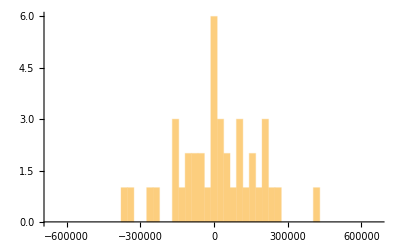

```mathematica
nbins=51;
Histogram[correlsHom,{-photonLength,photonLength,2photonLength/nbins}]
```

### Other / Additional

```mathematica
NCorrelationsPerThrow[data3Windowed,{0,2},{1}]
```

{{{0.0355893,0.00367901},{0.0782371,0.00529697}},{{0.0832788,0.00545151},{0.0407412,0.00397848}}}

```mathematica
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
TableForm[
NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,2]]
]
TableForm[
(#/Total[#,2])&@NCorrelationsPerThrow[data3Windowed,{0,2},{1}][[;;,;;,1]]
]
```

0.0355893 | 0.0782371
0.0832788 | 0.0407412

0.00367901 | 0.00529697
0.00545151 | 0.00397848

0.149632 | 0.328939
0.350137 | 0.171292

```mathematica
PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]]
```

{0.176429,0.0486276}

Ignoring Background effects

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@data3Windowed]
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@data3Windowed]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@data3Windowed]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@data3Windowed]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

12581

13906

345

397

0.0274223

0.0285488

0.96054

```mathematica
nEven=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;EvenQ[x]&&d==0]]/@data3Windowed]
nOdd=Total[Function[{m},Count[m[[;;,{1,4}]],{d_,x_}/;OddQ[x]&&d==2]]/@data3Windowed]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;EvenQ[x]&&y==x+1&&dx==0&&dy==2]]/@data3Windowed]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,{1,4}]],{{dx_,x_},{dy_,y_}}/;OddQ[x]&&y==x+1&&dx==2&&dy==0]]/@data3Windowed]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

9598

11267

243

234

0.0253178

0.0207686

1.21904

```mathematica
nEven=Total[Function[{m},Count[m[[;;,4]],x_/;EvenQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nOdd=Total[Function[{m},Count[m[[;;,4]],x_/;OddQ[x]]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

nOddAfterEven=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;EvenQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]
nEvenAfterOdd=Total[Function[{m},SequenceCount[m[[;;,4]],{x_,y_}/;OddQ[x]&&y==x+1]]/@#]&/@FilterByDetector[data3Windowed,{0,1}]

ηOddAfterEven=N@nOddAfterEven/nEven
ηEvenAfterOdd=N@nEvenAfterOdd/nOdd

ηRatio=ηOddAfterEven/ηEvenAfterOdd
```

{23069,5329}

{4153,17790}

{113,93}

{108,116}

{0.00489835,0.0174517}

{0.0260053,0.00652052}

{0.18836,2.67643}

## Tom' s Calcs

```mathematica
Δstirap=0;
Δzeeman = 12;
{75.25-Δstirap/2-Δzeeman, 75.25-Δstirap/2+Δzeeman}
80.5+Δstirap/2
```

{63.25,87.25}

80.5

```mathematica
2.7*(15/12.)
```

3.375